VALOR ÓTIMO = 75

Matriz de Decisão

| T1 | T2 | T3
Dev 1 | 1 | 0 | 0
Dev 2 | 0 | 0 | 1

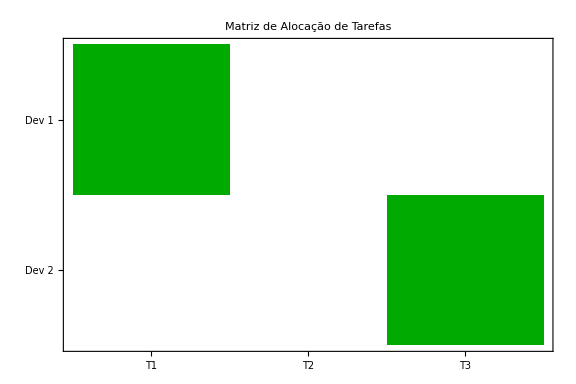

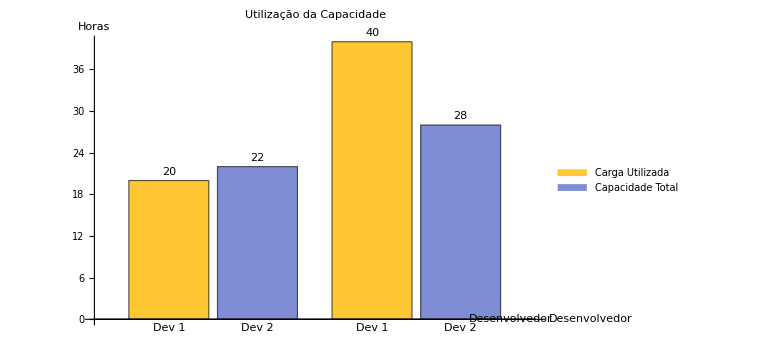

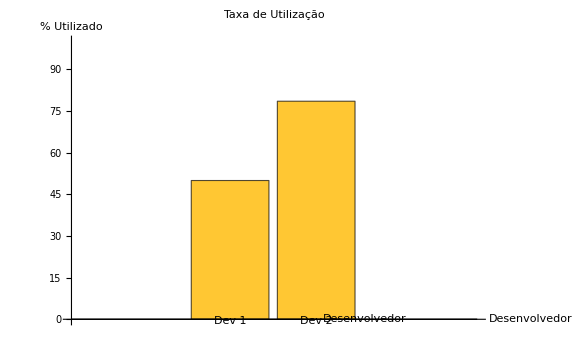

-Graphics3D-

```mathematica
(* ======================================*)(*DADOS*)(* ======================================*)ClearAll["Global`*"]

m=2;
n=3;

c={40,28};                  (*capacidade dos desenvolvedores*)
w={20,26,22};              (*esforço das tarefas*)
p={20,80,55};              (*prioridade das tarefas*)

s={{1,1,0},{0,0,1}};

d={{0,1,0},{0,0,0},{0,0,0}};

(* ======================================*)
(*VARIÁVEIS DE DECISÃO*)
(* ======================================*)

vars=Flatten@Table[x[i,j],{i,m},{j,n}];

(* ======================================*)
(*FUNÇÃO OBJETIVO*)
(* ======================================*)

obj=Sum[p[[j]]*x[i,j],{i,m},{j,n}];

(* ======================================*)
(*RESTRIÇÕES*)
(* ======================================*)

capConstr=Table[Sum[w[[j]]*x[i,j],{j,n}]<=c[[i]],{i,m}];

uniqConstr=Table[Sum[x[i,j],{i,m}]<=1,{j,n}];

skillConstr=Flatten@Table[x[i,j]<=s[[i,j]],{i,m},{j,n}];

depConstr=Flatten@Table[If[d[[j,jp]]==1,Sum[x[i,jp],{i,m}]<=Sum[x[i,j],{i,m}],Nothing],{j,n},{jp,n}];

bndConstr=Flatten@Table[0<=x[i,j]<=1,{i,m},{j,n}];

allConstr=Join[capConstr,uniqConstr,skillConstr,depConstr,bndConstr];

(* ======================================*)
(*SOLUÇÃO*)
(* ======================================*)

{maxVal,sol}=Maximize[{obj,allConstr},vars,Integers];

Print[Style["VALOR ÓTIMO = "<>ToString[maxVal],16,Bold,Darker[Blue]]];

(* ======================================*)
(*MATRIZ DE DECISÃO*)
(* ======================================*)

xSol=Table[x[i,j]/. sol,{i,m},{j,n}];

Print[Style["Matriz de Decisão",14,Bold]];

Grid[Join[{Prepend[Table["T"<>ToString[j],{j,n}],""]},Table[Prepend[xSol[[i]],"Dev "<>ToString[i]],{i,m}]],Frame->All,Background->{None,{LightGray,White}}]

(* ======================================*)
(*MÉTRICAS*)
(* ======================================*)

cargaUsada=Table[Sum[w[[j]]*xSol[[i,j]],{j,n}],{i,m}];

eficiencia=Table[100*cargaUsada[[i]]/c[[i]],{i,m}];

(* ======================================*)
(*GRÁFICO 1-HEATMAP*)
(* ======================================*)

MatrixPlot[xSol,FrameTicks->{Table[{i,"Dev "<>ToString[i]},{i,m}],Table[{j,"T"<>ToString[j]},{j,n}]},ColorRules->{0->White,1->Darker[Green]},PlotLabel->Style["Matriz de Alocação de Tarefas",16,Bold],ImageSize->Large]

(* ======================================*)
(*GRÁFICO 2-CAPACIDADE*)
(* ======================================*)

BarChart[{cargaUsada,c},ChartLayout->"Grouped",ChartLegends->{"Carga Utilizada","Capacidade Total"},ChartLabels->Placed[{"Dev 1","Dev 2"},Below],LabelingFunction->Above,PlotLabel->Style["Utilização da Capacidade",16,Bold],AxesLabel->{"Desenvolvedor","Horas"},ImageSize->Large]

(* ======================================*)
(*GRÁFICO 3-EFICIÊNCIA*)
(* ======================================*)

BarChart[eficiencia,ChartLabels->{"Dev 1","Dev 2"},LabelingFunction->(ToString[NumberForm[#1,{4,1}]]<>"%"&),PlotRange->{0,100},PlotLabel->Style["Taxa de Utilização",16,Bold],AxesLabel->{"Desenvolvedor","% Utilizado"},ImageSize->Large]

(* ======================================*)
(*GRÁFICO 4-VISUALIZAÇÃO 3D*)
(* ======================================*)

Graphics3D[Table[{If[xSol[[i,j]]==1,Darker[Green],LightGray],Cuboid[{j-0.4,i-0.4,0},{j+0.4,i+0.4,xSol[[i,j]]}]},{i,m},{j,n}],Axes->True,AxesLabel->{Style["Tarefa",Bold],Style["Desenvolvedor",Bold],Style["Selecionada",Bold]},BoxRatios->{n,m,1},PlotLabel->Style["Alocação 3D das Tarefas",16,Bold],ImageSize->Large]
```